```mathematica
Options[FredholmKind2]={Method->Automatic};
FredholmKind2[{a_,b_,lambda_,k_,g_},n_?IntegerQ,OptionsPattern[]]:=Block[{step,SI,GI,KMatrix,W,DMatrix,f,deltaX,delta},step=(b-a)/n;
SI=Range[a,b,step];
GI=g/@SI;
KMatrix=Outer[k,SI,SI];
W={step/2}~Join~ConstantArray[step,n-1]~Join~{step/2};
DMatrix=DiagonalMatrix[W];
f=If[OptionValue[Method]===NIntegrate,deltaX[x_?NumericQ]:=W.(k[x,#]&/@SI)-NIntegrate[k[x,y],{y,a,b},AccuracyGoal->4];
(*If the integral is expensive ParallelMap is an option here*)delta=deltaX/@SI;
Interpolation[Transpose@{SI,LinearSolve[IdentityMatrix[n+1]+lambda*(DiagonalMatrix[delta]-KMatrix.DMatrix),GI]}],Interpolation[Transpose@{SI,LinearSolve[IdentityMatrix[n+1]-lambda*(KMatrix.DMatrix),GI]}]];
f]
```

```mathematica
α=2.;u0=1.*10^-8;r1=50.;r2=u0;m=1;ℏ=1;
V[r_]=-1/r-(1.0415223038416566 ⅇ^(-0.9990999998788636 r))/r;
(*e=10^-10;*)k=√(2e);l=0;
```

```mathematica
Clear["Global`*"]
```

```mathematica
equ={Al[r]==SphericalBesselJ[l,k r]-(2m I k)/ℏ^2 Integrate[SphericalBesselJ[l,k R]V[R]Al[R] R^2,{R,0,∞}]};
```

```mathematica
V[R] R^2
```

(-1/R-(1.04152 ⅇ^(-0.9991 R))/R) R^2

```mathematica
Simplify[(-1/R-(1.0415223038416566 ⅇ^(-0.9990999998788636 R))/R) R^2]
```

(-1.-1.04152 ⅇ^(-0.9991 R)) R

```mathematica
(*SphericalBesselJ[l,k r]*)SphericalHankelH1[l,k R](*V[R] R^2*)
```

```mathematica
FunctionExpand[SphericalBesselJ[l,k R]SphericalHankelH1[l,k r]V[R] R^2]
```

((0.+0.5 ⅈ) ⅇ^(ⅈ √2 √e r-0.9991 R) (1.04152+ⅇ^(0.9991 R)) Sin[√2 √e R])/(e r)

```mathematica
FunctionExpand[SphericalBesselJ[l,k r]SphericalHankelH1[l,k R]]
```

BesselJ[1/2 (1+2 l),k r] ((π BesselJ[1/2 (1+2 l),k R])/(2 √(k r) √(k R))+(ⅈ π BesselY[1/2 (1+2 l),k R])/(2 √(k r) √(k R)))

```mathematica
FunctionExpand[SphericalHankelH1[l,k R]]
```

-(ⅈ ⅇ^(ⅈ √2 √e R))/(√2 √e R)

```mathematica
Simplify[If[r>R,SphericalBesselJ[l,k R]SphericalHankelH1[l,k r],SphericalBesselJ[l,k r]SphericalHankelH1[l,k R]]V[R] R^2]
```

-1. ⅇ^(-0.9991 R) (1.04152+ⅇ^(0.9991 R)) R If[r>R,SphericalBesselJ[l,k R] SphericalHankelH1[l,k r],SphericalBesselJ[l,k r] SphericalHankelH1[l,k R]]

```mathematica
n=5000;a=1.*10^-5;b=50.;λ=-(2m I  k)/ℏ^2;Kpart[r_,R_]:=If[r>R,SphericalBesselJ[l,k R]SphericalHankelH1[l,k r],SphericalBesselJ[l,k r]SphericalHankelH1[l,k R]]V[R] R^2;
Gpart[r_]:=SphericalBesselJ[l,k r];
Al1=Block[{e=0.003},FredholmKind2[{a,b,λ,Kpart,Gpart},n,Method->NIntegrate]]
```

InterpolatingFunction[{{0.00001, 50.}}, <>]

```mathematica
Block[{r=0.01,e=0.003},-Al1[r]+SphericalBesselJ[l,k r]-(2m I k)/ℏ^2 NIntegrate[If[r>R,SphericalBesselJ[l,k R]SphericalHankelH1[l,k r],SphericalBesselJ[l,k r]SphericalHankelH1[l,k R]]V[R]Al1[R] R^2,{R,a,b}]]
```

0.0000575269-0.00112002 ⅈ

```mathematica
Al2[x_]=Re[Al1[x]]+Im[Al1[x]]
```

Im[InterpolatingFunction[{{0.00001, 50.}}, <>][x]]+Re[InterpolatingFunction[{{0.00001, 50.}}, <>][x]]

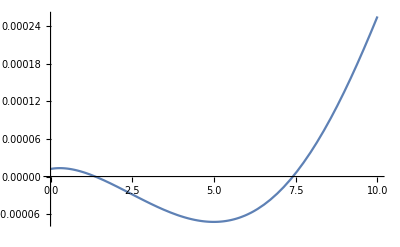

```mathematica
Plot[Al2[x],{x,0,10}]
```

```mathematica
Block[{r=0.5,e=0.003},-Al2[r]+SphericalBesselJ[l,k r]-(2m I k)/ℏ^2 NIntegrate[If[r>R,SphericalBesselJ[l,k R]SphericalHankelH1[l,k r],SphericalBesselJ[l,k r]SphericalHankelH1[l,k R]]V[R]Al2[R] R^2,{R,a,b}]]
```

-0.7026-0.670808 ⅈ

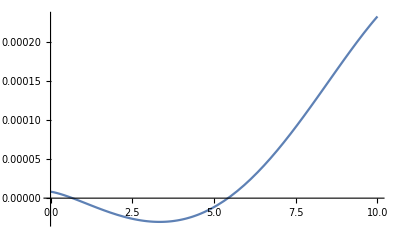

```mathematica
Plot[Re[Al1[x]],{x,0,10}]
```

```mathematica
Block[{e=0.003},FindRoot[E^(I δ)Sin[δ]/k==-(2 m/ℏ^2)NIntegrate[SphericalBesselJ[0,k r]Al1[r] V[r] r^2,{r,0,50},AccuracyGoal->10,MaxRecursion->12],{δ,0,1},MaxIterations->10000]]
```

{δ→1.63488+0.0000821229 ⅈ}

```mathematica
-2.0491888114767867+π
```

1.0924

```mathematica
po[er_][x_]:=Sin[er x]
```

```mathematica
po[er]'[0.2]
```

er Cos[0.2 er]

```mathematica
D[SphericalBesselJ[0,r],r]
```

-SphericalBesselJ[0,r]/(2 r)+1/2 (SphericalBesselJ[-1,r]-SphericalBesselJ[1,r])